## Project 2

#### 1

A

```mathematica
A1=({{1/5000, 0}, {0, 1/5000}})*({{10000, 0}, {0, 10000}})
```

{{2,0},{0,2}}

B

```mathematica
Eigenvalues[A1]
```

{2,2}

```mathematica
fa1=√2//N
```

1.41421

```mathematica
2π/fa1
```

4.44288

C

A period of 4.44 seconds is outside of the “danger zone” of 2-3s

#### 2

A)

```mathematica
M:=({{20000, 0, 0}, {0, 20000, 0}, {0, 0, 20000}})
```

```mathematica
K:=({{50000, 0, 0}, {0, 50000, 0}, {0, 0, 50000}})
```

```mathematica
A:=({{1/20000, 0, 0}, {0, 1/20000, 0}, {0, 0, 1/20000}})*({{50000, 0, 0}, {0, 50000, 0}, {0, 0, 50000}})
```

```mathematica
A
```

{{5/2,0,0},{0,5/2,0},{0,0,5/2}}

B)

```mathematica
Eigenvalues[A]
```

{5/2,5/2,5/2}

```mathematica
fb=√(5/2)//N
```

1.58114

```mathematica
2π/fb
```

3.97384

C)

```mathematica
ys:=({{1/20000, 0, 0}, {0, 1/20000, 0}, {0, 0, 1/20000}})*({{500000, 0, 0}, {0, 500000, 0}, {0, 0, 500000}})
```

```mathematica
ys
```

{{25,0,0},{0,25,0},{0,0,25}}

```mathematica
Eigenvalues[ys]
```

{25,25,25}

```mathematica
fc=√25//N
```

5.

```mathematica
pc=2π/fc
```

1.25664

D)

```mathematica
f[a_]:=({{1/20000, 0, 0}, {0, 1/20000, 0}, {0, 0, 1/20000}})*({{a, 0, 0}, {0, a, 0}, {0, 0, a}})
```

```mathematica
Function[a,{{1/20000,0,0},{0,1/20000,0},{0,0,1/20000}} {{a,0,0},{0,a,0},{0,0,a}}]
```

Function[a,{{1/20000,0,0},{0,1/20000,0},{0,0,1/20000}} {{a,0,0},{0,a,0},{0,0,a}}]

```mathematica
f[500000]
```

{{25,0,0},{0,25,0},{0,0,25}}

```mathematica
Solve[Eigenvalues[f[a]]=={π^2,π^2,π^2},a]//N
```

{{a→197392.}}

```mathematica
Solve[Eigenvalues[f[a]]=={π^2/4,π^2/4,π^2/4},a]//N
```

{{a→49348.}}

gives range of “dangerous” values

```mathematica
49348/50000//N
```

0.98696

```mathematica
197392/50000//N
```

3.94784

E)

```mathematica
g[m_]:=({{50000/m, 0, 0}, {0, 50000/m, 0}, {0, 0, 50000/m}})
```

```mathematica
Function[m,{{50000/m,0,0},{0,50000/m,0},{0,0,50000/m}}]
```

Function[m,{{50000/m,0,0},{0,50000/m,0},{0,0,50000/m}}]

```mathematica
Eigenvalues[g[m]]
```

{50000/m,50000/m,50000/m}

```mathematica
fs[m_]:=√(50000/m)//N
```

```mathematica
ps[m_]:=2π/(√(50000/m))
```

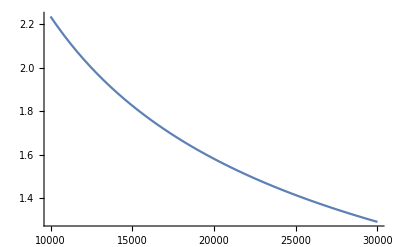

```mathematica
Plot[fs[m],{m,10000,30000}]
```

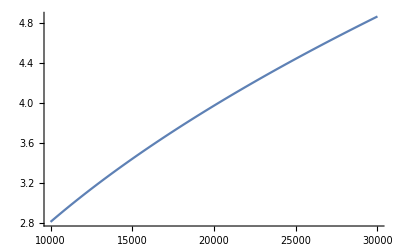

```mathematica
Plot[ps[m],{m,10000,30000}]
```